## 第1章 统计学习及监督概率

## 例1.1

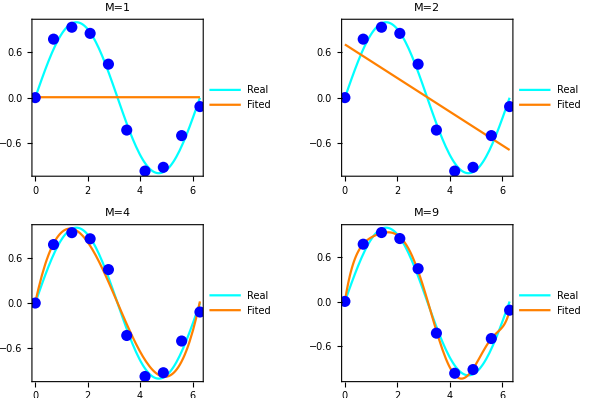

```mathematica
Module[{pts={#,Sin[#]+RandomReal[{-0.15,0.15}]}&/@Table[(2π)/9 i,{i,0,9}],swatchLegent},SeedRandom[111];
swatchLegend[name_]:=Placed[SwatchLegend[name,LegendMarkers->"Line",LegendFunction->"Frame",LegendLayout->"Column"],{{0.95,0.95},{1,1}}];
GraphicsGrid[Partition[Plot[{Sin[x],Evaluate@Fit[pts,Table[x^i,{i,0,#}],x]},{x,0,2π},Epilog->{Blue,PointSize@0.02,Point@pts},PlotStyle->{Cyan,Orange},PlotLegends->swatchLegend[{"Real","Fited"}],Frame->True,PlotLabel->Style["M="<>ToString[#+1],Bold]]&/@{0,1,3,8},2,2],ImageSize->600]]
```

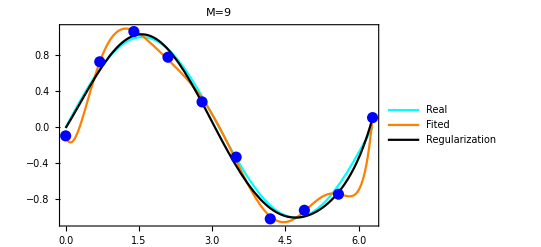

```mathematica
Module[{pts={#,Sin[#]+RandomReal[{-0.15,0.15}]}&/@Table[(2π)/9 i,{i,0,9}],swatchLegent},SeedRandom[111];
swatchLegend[name_]:=Placed[SwatchLegend[name,LegendMarkers->"Line",LegendFunction->"Frame",LegendLayout->"Column"],{{0.95,0.95},{1,1}}];Plot[{Sin[x],Evaluate@Fit[pts,Table[x^i,{i,0,8}],x],Evaluate@Fit[pts,Table[x^i,{i,0,8}],x,FitRegularization->{"L2",0.05}]},{x,0,2π},Epilog->{Blue,PointSize@0.02,Point@pts},PlotStyle->{Cyan,Orange,Black},PlotLegends->swatchLegend[{"Real","Fited","Regularization"}],Frame->True,PlotLabel->Style["M="<>ToString[8+1],Bold]]]
```

## 第2章 感知机

## 梯度下降法

```mathematica
Manipulate[Module[{f,θ0=1,ϵ=0.001,xList},f[θ_]:=θ^2;
xList=NestWhileList[#1-η f'[#1]&,θ0,Abs[f[#1]-f[#2]]>ϵ&,2];
Plot[f[θ],{θ,-1.1,1.1},Epilog->{Red,Arrowheads@Medium,Arrow[Partition[{xList,f/@xList}ᵀ,2,1]],PointSize@0.02,Black,Point[{θ0,f[θ0]}]},PlotLabel->Style[StringForm["梯度下降法，学习率η=``.",η],Red,20],ImageSize->Medium]],{{η,0.05,"学习率η"},Range[0.05,1,0.05],ControlType->Slider,Appearance->"Labeled"},SaveDefinitions->True]
```

## 例2.1

```mathematica
Manipulate[DynamicModule[{rule=<|{3,3}->1,{4,3}->1,{1,1}->-1|>,η =1,X,y,ruleData,w,b,test,data,x},
X=Keys@rule;
y=Values@rule;
ruleData={X,y}ᵀ;
{w,b}={{0,0},0};
test[para_List]:=MemberQ[#[[2]](para[[1]].#[[1]]+para[[2]])≤0&/@ruleData,True];(* 测试数据中是否含有误分类点 *)
data[para_List]:=SelectFirst[ruleData,#[[2]](para[[1]].#[[1]]+para[[2]])≤0&];(* 选出不能正确分类的点 *)
DynamicWrapper[DynamicWrapper[Dynamic@Show[p1,p2],p1=ListPlot[Values@GroupBy[ruleData,Last,#[[All,1]]&],PlotStyle->PointSize@0.025]],
wbList=NestWhileList[(datai=data[#];{#[[1]]+η datai[[1]]datai[[2]],#[[2]]+η  datai[[2]]})&,{w,b},test[#]&](* wbList这个函数想了很久经网友指点️才写来 *);
p2=Plot[Evaluate[-(wb[[1,1]]x+wb[[2]])/wb[[1,2]]],{x,0,4},PlotStyle->Red]]],{{wb,Last@wbList,"w、b参数"},wbList,ControlType->PopupMenu}]
(*使用了动态封装，注意wbList的位置 *)
(* 从结果看感知机效果并不好 *)
```

## 例 2.2

```mathematica
Module[{rule=<|{3,3}->1,{4,3}->1,{1,1}->-1|>,X,y,ruleData,α,b,G},
X=Keys@rule;
y=Values@rule;
ruleData={X,y}ᵀ;
α=Array[0&,Length@y];
b=0;
G=Table[Dot[X[[i]],X[[j]]ᵀ],{i,1,Length@y},{j,1,Length@y}]]
```

{{18,21,6},{21,25,7},{6,7,2}}

## 第3章 k近临法

## 临近法模型

```mathematica
Manipulate[
DynamicModule[{sites,mf,x,y},SeedRandom[δ];
sites=RandomPoint[reg,n];
mf=(*RegionMemberFunction*)RegionMember[reg];
DynamicWrapper[DynamicWrapper[Dynamic@Show[p2,p1],p1=Graphics[{PointSize[.01],Point/@sites}]],p2=RegionPlot[mf[{x,y}],{x,-1,1},{y,-1,1},PlotRange->1.1,PlotPoints->100,PerformanceGoal->"Speed",BoundaryStyle->Opacity[0],Mesh->{n},
MeshFunctions->{First@Nearest[sites->Automatic,{#1,#2},DistanceFunction->df,Method->"KDtree"]&},
MeshStyle->Black,Background->Darker[Gray,.25],
MeshShading->(Hue[#]&/@Range[0.,1,1/(n+1)]),Frame->False,Axes->False,ImageSize->1.1{400,400},PerformanceGoal->"Speed"]]],
{{n,16,"n="},Range[2,24]},
Button["new set of sites",δ=δ+1(*trigger for SeedRandom*)],
{{reg,Disk[],"Region"},{Rectangle[{-1,-1},{1,1}]->"square",Parallelogram[{-1,-1},{{1.75,0.},{.25,2.}}]->"parallelogram",Disk[]->"disk",Annulus[]->"annulus",StadiumShape[{{-.5,0},{.5,0}},.5]->"stadium",RegularPolygon[3]->"triangle",RegularPolygon[{1,0},5]->"pentagon"},PopupMenu},
"distance function",{{df,EuclideanDistance,""},
{ManhattanDistance->"Manhattan",ChessboardDistance->"Chessboard",EuclideanDistance->"Euclidean"},PopupMenu},
{{δ,123},None},
ControlPlacement->Left,SaveDefinitions->True ](* wolfram Demo 文档修改 *)
```

## 例3.1

```mathematica
X={{1,1},{5,1},{4,4}};
L[u_,v_,p_]:=N@(Sum[Abs[u[[l]]-v[[l]]]^p,{l,1,Length[u]}]^(1/p));
L[X[[1]],X[[2]],#]&/@{1,2,3,4}
L[X[[1]],X[[3]],#]&/@{1,2,3,4}
```

{4.,4.,4.,4.}

{6.,4.24264,3.77976,3.56762}

## 例3.2

```mathematica
T={{2,3},{5,4},{9,6},{4,7},{8,1},{7,2}};
```

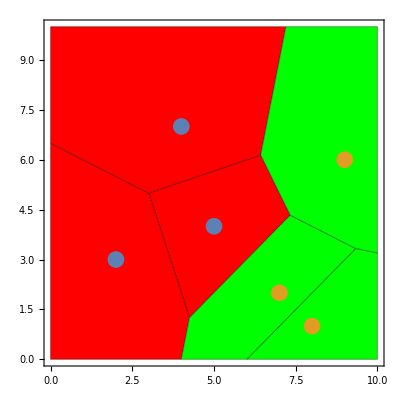

```mathematica
fc=FindClusters[T,2,Method->"KMeans"];
 MapIndexed[Flatten[{#,First@#2}]&,fc,{2}];
Show[ListDensityPlot[ Flatten[MapIndexed[Flatten[{#,First@#2}]&,fc,{2}],{1,2}],PlotRange->{{0,10},{0,10}},InterpolationOrder->0,ColorFunction->(Hue[#/(2+1)]&),Mesh->All],ListPlot[fc,PlotStyle->PointSize@0.03]]
```

## 第4章 朴素贝叶斯法的参数估计

## 例 4.1

```mathematica
Module[{X={{1,S},{1,M},{1,M},{1,S},{1,S},{2,S},{2,M},{2,M},{2,L},{2,L},{3,L},{3,M},{3,M},{3,L},{3,L}},
Y={-1,-1,1,1,-1,-1,-1,1,1,1,1,1,1,1,-1},PY,XY,X1Y1,X2Y2},
Ck=(Counts@Y)/(Total@*Counts@Y);(*先验概率*)
XY={X,Y}ᵀ;(*先列表元素，然后通过GroupBy分类形成Association结构*)
X1giveCk=GroupBy[XY,Last(*Ck*)->First(*特征*),Counts[#[[All,1]]]/(Total@Counts[#[[All,2]]])&];(*条件概率,给定Ck条件下的X1特征的概率*)
X2giveCk=GroupBy[XY,Last(*Ck*)->First(*特征*),Counts[#[[All,2]]]/(Total@Counts[#[[All,2]]])&];(*条件概率，给定Ck条件下的X1特征的概率*)
Ck[[Key[#]]]X1giveCk[[Key[#],Key[2]]]X2giveCk[[Key[#],Key[S]]]&/@Keys[Ck]](*多个Key取层级value*)(*确定类别*)
```

{1/15,1/45}

## 例 4.2

```mathematica
Module[{X={{1,S},{1,M},{1,M},{1,S},{1,S},{2,S},{2,M},{2,M},{2,L},{2,L},{3,L},{3,M},{3,M},{3,L},{3,L}},
Y={-1,-1,1,1,-1,-1,-1,1,1,1,1,1,1,1,-1},kY,PY,kX1,kX2,XY,X1Y1,X2Y2},
k=Length@Counts@Y;
Ck=(Counts@Y+1)/(Total@*Counts@Y+k);(*先验概率*)
n1=Length@Counts@X[[All,1]];(* 第一个特征有几个特征值 *)
n2=Length@Counts@X[[All,2]];(* 第二个特征有几个特征值 *)
XY={X,Y}ᵀ;(* 包含分类信息的数据集合 *)
X1giveCk=GroupBy[XY,Last(*Ck*)->First(*特征*),(Counts[#[[All,1]]]+1)/(Total@Counts[#[[All,1]]]+n1)&];(*条件概率,给定Ck条件下的第一个特征的概率*)
X2giveCk=GroupBy[XY,Last(*Ck*)->First(*特征*),(Counts[#[[All,2]]]+1)/(Total@Counts[#[[All,2]]]+n2)&];(*条件概率,给定Ck条件下的第二个特征的概率*)
Ck[[Key[#]]]X1giveCk[[Key[#],Key[2]]]X2giveCk[[Key[#],Key[S]]]&/@Keys[Ck]]
```

{28/459,5/153}

## 第5章 决策树

## Tree

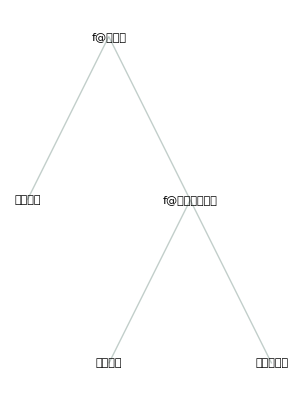

```mathematica
RulesTree["f@有工作"->{"同意贷款","f@有自己的房子"->{"同意贷款","不同意贷款"} }](*RulesTree 为 Mathematica12.3的新函数*)
(* 是否贷款["有工作"_,"有自己的房子"_]:=If["有工作"==True,"同意贷款",If["有自己的房子"==True,"同意贷款","不同意贷款"]] *)
```

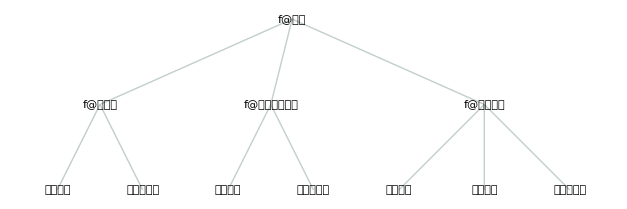

```mathematica
RulesTree["f@年龄"->{"f@有工作"->{"同意贷款","不同意贷款"},"f@有自己的房子"->{"同意贷款","不同意贷款"},"f@信贷情况"->{"同意贷款","同意贷款","不同意贷款"}}](*RulesTree 为 Mathematica12.3的新函数*)
```

## 例 5.1

年龄 | 有工作 | 有自己的房子 | 信贷情况 | 类别
青年 | 否 | 否 | 一般 | 否
青年 | 否 | 否 | 好 | 否
青年 | 是 | 否 | 好 | 是
青年 | 是 | 是 | 一般 | 是
青年 | 否 | 否 | 一般 | 否
中年 | 否 | 否 | 一般 | 否
中年 | 否 | 否 | 好 | 否
中年 | 是 | 是 | 好 | 是
中年 | 否 | 是 | 非常好 | 是
中年 | 否 | 是 | 非常好 | 是
老年 | 否 | 是 | 非常好 | 是
老年 | 否 | 是 | 好 | 是
老年 | 是 | 否 | 好 | 是
老年 | 是 | 否 | 非常好 | 是
老年 | 否 | 否 | 一般 | 否

<|否→{否,否,是,否,否,否,是,是,否},是→{是,是,是,是,是,是}|>

{{{青年,否,一般},否},{{青年,否,好},否},{{青年,是,好},是},{{青年,否,一般},否},{{中年,否,一般},否},{{中年,否,好},否},{{老年,是,好},是},{{老年,是,非常好},是},{{老年,否,一般},否}}

<|否→{否,否,否,否,否,否},是→{是,是,是}|>

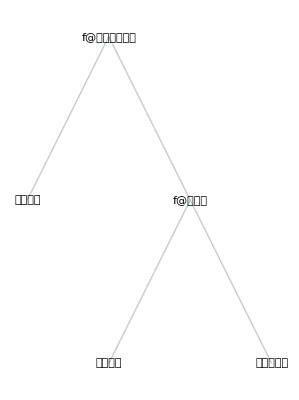

```mathematica
X={{"青年","青年","青年","青年","青年","中年","中年","中年","中年","中年","老年","老年","老年","老年","老年"},{"否","否","是","是","否","否","否","是","否","否","否","否","是","是","否"},{"否","否","否","是","否","否","否","是","是","是","是","是","否","否","否"},{"一般","好","好","一般","一般","一般","好","好","非常好","非常好","非常好","好","好","非常好","一般"}};  (*实例X*)
A={"年龄","有工作","有自己的房子","信贷情况"};(* 4个特征A *)
Y={"否","否","是","是","否","否","否","是","是","是","是","是","是","是","否"};
XY={Xᵀ,Y}ᵀ ;
Join[X,{Y}]ᵀ//TableForm[#,TableHeadings->{None,Join[A,{"类别"}]},TableAlignments->Center]&
GroupBy[XY, (#[[1,3]]&)->Last](* 有自己房子特征作为是否房贷的标准，有自己的房子可以放贷，没有自己房子分情况 *)
XY=Select[XY,#[[1,3]]=="否"&];(* 选择没有自己房子的子特征列表 *)
XYA3=MapAt[Delete[#,3]&,XY,{All,1}](*  删除有自己房子的特征元素 *)
GroupBy[XYA3, (#[[1,2]]&)->Last](* 有工作特征作为是否房贷的标准，有工作可以放贷，没有工作不能房贷 *)
RulesTree["f@有自己的房子"->{"同意贷款","f@有工作"->{"同意贷款","不同意贷款"}}]
```

## 例 5.2

```mathematica
Module[{X={{"青年","青年","青年","青年","青年","中年","中年","中年","中年","中年","老年","老年","老年","老年","老年"},{"否","否","是","是","否","否","否","是","否","否","否","否","是","是","否"},{"否","否","否","是","否","否","否","是","是","是","是","是","否","否","否"},{"一般","好","好","一般","一般","一般","好","好","非常好","非常好","非常好","好","好","非常好","一般"}},  (*实例X*)
A={"年龄","有工作","有自己的房子","信贷情况"},(* 4个特征A *)
Y={"否","否","是","是","否","否","否","是","是","是","是","是","是","是","否"}(* 2个分类 *)},
n=Length@Keys@Counts[Y];
XY={Xᵀ,Y}ᵀ  (* 包含分类信息的数据集合 *);
HD=N@Total@(-# Log[2,#]&/@((Values@Counts[Y])/(Total@Counts[Y])))(*数据集D的信息经验熵H(D) *);
pDi=#/Total[#]&/@(Counts/@X) (*Subscript[样本子集D, i] 的概率*);
AgiveCk=Function[x,GroupBy[XY,Last->First,Counts[#[[All,x]]]&]]/@Range[Length@A](* Subscript[D, ik] 样本 *);
pAgiveCk=Function[x,Map[#/Total[#]&,x]]/@(Merge[#,Identity]&/@Values@AgiveCk)(*(|Subscript[D, ik]|)/(|Subscript[D, i]|)概率 *);
HDik=MapThread[N[-#  #2Log[2,#2]]&,{pDi,pAgiveCk}](* 计算 (|Subscript[D, i]|)/(|D|)H(Subscript[D, ik])条件经验熵 *);
HDgiveA=Total@*Flatten/@(Values@HDik)(* ∑_(i=1)^n H(Subscript[D, ik]) *);
data=Dataset@{AssociationThread[A,(HD-HDgiveA)],(AssociationThread[A,(HD-HDgiveA)](* 信息增益 *))/(AssociationThread[A,N@Total[-# Log[2,#]]&/@pDi](*特征A的熵：Subscript[H, A](D)*))(*信息增益比*)};
dataNew=Dataset@AssociationThread[{"信息增益","信息增益比"},(AssociationThread[First@Normal@data[Keys],#]&/@Normal@data[Values])]]
(*  信息增益: 第一位特征值是：有自己的工作，第二位特征值为：信贷情况*)
(*  信息增益比: 第一位特征值是：有自己的工作，第二位特征值为：有工作  *)
(* 总体而言代码不太好写 *)
```

## 例 5.3

```mathematica
Module[{X={{"青年","青年","青年","青年","青年","中年","中年","中年","中年","中年","老年","老年","老年","老年","老年"},{"否","否","是","是","否","否","否","是","否","否","否","否","是","是","否"},{"否","否","否","是","否","否","否","是","是","是","是","是","否","否","否"},{"一般","好","好","一般","一般","一般","好","好","非常好","非常好","非常好","好","好","非常好","一般"}},  (*实例X*)
A={"年龄","有工作","有自己的房子","信贷情况"},(* 4个特征A *)
Y={"否","否","是","是","否","否","否","是","是","是","是","是","是","是","否"}(* 2个分类 *)},
XY={Xᵀ,Y}ᵀ ; 
n=Length@Keys@Counts[Y];
GroupBy[XY, (#[[1,3]]&)->Last](* 在例2.1基础上选第三个特征A3：有自己的房子,它将训练集划分为2个子集,选子集合"否D2"进行计算 *);
XY=Select[XY,#[[1,3]]=="否"&];
XY=MapAt[Delete[#,3]&,XY,{All,1}](*去掉是否有房子这个特征*);
X=XY[[All,1]]ᵀ(*数据从新生成*);
Y=XY[[All,-1]](*数据从新生成*);
A=Drop[A,{3}](*数据从新生成*);
HD=N@Total@(-# Log[2,#]&/@((Values@Counts[XY[[All,-1]]])/(Total@Counts[XY[[All,-1]]])))(*数据集D的信息经验熵H(D2) *);
pDi=#/Total[#]&/@(Counts/@X) (*Subscript[样本子集D, i] 的概率*);
AgiveCk=Function[x,GroupBy[XY,Last->First,Counts[#[[All,x]]]&]]/@Range[Length@A](* Subscript[D, ik] 样本 *);
pAgiveCk=Function[x,Map[#/Total[#]&,x]]/@(Merge[#,Identity]&/@Values@AgiveCk)(*(|Subscript[D, ik]|)/(|Subscript[D, i]|)概率 *);
HDik=MapThread[N[-#  #2Log[2,#2]]&,{pDi,pAgiveCk}](* 计算 (|Subscript[D, i]|)/(|D|)H(Subscript[D, ik])条件经验熵 *);
HDgiveA=Total@*Flatten/@(Values@HDik)(* ∑_(i=1)^n H(Subscript[D, ik]) *);
data=Dataset@{AssociationThread[A,(HD-HDgiveA)],(AssociationThread[A,(HD-HDgiveA)](* 信息增益 *))/(AssociationThread[A,N@Total[-# Log[2,#]]&/@pDi](*特征A的熵：Subscript[H, A](D)*))(*信息增益比*)};
dataNew=Dataset@AssociationThread[{"信息增益","信息增益比"},(AssociationThread[First@Normal@data[Keys],#]&/@Normal@data[Values])]]
```

```mathematica
RulesTree["f@有自己的房子"->{"同意贷款","f@有工作"->{"同意贷款","不同意贷款"}}](*参考例题5.1、5.2*)
```

-Graphics-

## 第6章 逻辑斯蒂回归与最大熵模型

## 例 6.1

```mathematica
X={a,b,c,d,e};
Solve[{Total@X==1,Equal@@X},X](* 最大熵模型隐含的条件是未含约束条件的变量都相等（均衡） *)
Solve[{Total@X==1,a+b==3/10,Equal@@{a,b},Equal@@{c,d,e}},X]
Solve[{Total@X==1,a+c==1/2,a+b==3/10,Equal@@{c,d,e}},X]
```

{{a→1/5,b→1/5,c→1/5,d→1/5,e→1/5}}

{{a→3/20,b→3/20,c→7/30,d→7/30,e→7/30}}

{{a→4/15,b→1/30,c→7/30,d→7/30,e→7/30}}

## 例6.2

```mathematica
FindMaximum[{-(y1*Log[y1]+y2*Log[y2]+y3*Log[y3]+y4*Log[y4]+y5*Log[y5]),y1+y2==3/10,y1+y2+y3+y4+y5==1},{y1,y2,y3,y4,y5}](*显式求最大熵，利用Mathematica求最值的优势 *)
```

{1.58784,{y1→0.15,y2→0.15,y3→0.233334,y4→0.233334,y5→0.233334}}

```mathematica
Clear["Global`*"]
f[y1_,y2_,y3_,y4_,y5_,w0_,w1_]:=-(y1*Log[y1]+y2*Log[y2]+y3*Log[y3]+y4*Log[y4]+y5*Log[y5])+w0(y1+y2-3/10)+w1(y1+y2+y3+y4+y5-1);(* 拉格朗日对偶性求方程 *)
(*原理详见： https://www.zhihu.com/question/38586401 *)
f1[y1_,y2_,y3_,y4_,y5_]:=-(y1*Log[y1]+y2*Log[y2]+y3*Log[y3]+y4*Log[y4]+y5*Log[y5]);
st1[y1_,y2_]:=w0(y1+y2-3/10);
st2[y1_,y2_]:=w1(y1+y2+y3+y4+y5-1);
st2[y1_,y2_]:=0;
st2[y1_,y2_]:=0;
(*书上求最值方法*)
```

## 第7章 支持向量机

## Mathematica支持向量机参数表达

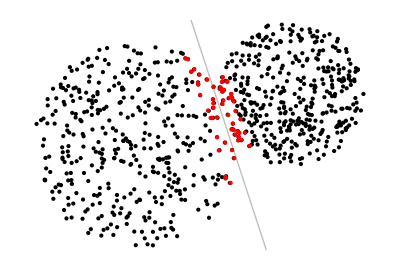

-Graphics3D-

```mathematica
unstandardize[point_,sd_,mu_]:=point*sd+mu;
getvectors[cf_ClassifierFunction,data_]:=With[{p=data[[All,1]]},With[{sd=StandardDeviation[p],mu=Mean[p]},unstandardize[#,sd,mu]&/@cf[[1]]["Model"]["TrainedModel"][[1]]["supportVectors"]]]
getplane[svmcf_ClassifierFunction,data_]:=With[{tm=svmcf[[1]]["Model"]["TrainedModel"][[1]],points=data[[All,1]]},Module[{sv=tm["supportVectors"],svc=tm["supportVectorCoefficients"],sd=StandardDeviation[points],mu=Mean[points],dim=Length[points[[1]]],vecs,offset},vecs=Rest[RotationMatrix[{svc.sv,PadRight[{1},dim]}].IdentityMatrix[dim]];
offset=With[{vars=Array[x,dim]},Values@First@FindInstance[vars.(svc.sv)==tm["rho"],vars]];
vecs=sd*#&/@vecs;
offset=unstandardize[offset,sd,mu];
If[dim>2,InfinitePlane[offset,vecs],InfiniteLine[offset,First[vecs]]]]]
(*Test the 2D case*)
SeedRandom[123];
training2D=Join[Thread[RandomPoint[Disk[],400]->0],Thread[RandomPoint[Disk[{1.5,0.5},.7],400]->1]];
cf2D=Classify[training2D,Method->{"SupportVectorMachine","KernelType"->"Linear"}];
Graphics[{Point[training2D[[All,1]]],Red,PointSize[Large],Point[getvectors[cf2D,training2D]],Opacity[.5],Gray,getplane[cf2D,training2D]}]

(*Test the 3D case*)
training3D=Join[Thread[RandomPoint[Ball[],400]->0],Thread[RandomPoint[Ball[{1.5,0.5,0.8},.7],400]->1]];
cf3D=Classify[training3D,Method->{"SupportVectorMachine","KernelType"->"Linear"}];
Graphics3D[{Point[training3D[[All,1]]],Red,PointSize[Large],Point[getvectors[cf3D,training3D]],Opacity[.5],Gray,getplane[cf3D,training3D]},BoxRatios->1,PlotRange->{{-2,2},{-2,2},{-2,2}}]
(* mathematica.stackexchange上面的代码 *)
(* Mathematica支持向量机参数w、b不太容易获取 *)
```

## 例 7.1

```mathematica
Module[{training={{3,3}->1,{4,3}->1,{1,1}->-1},para},
para=Last@Minimize[{1/2(w1^2+w2^2),Sequence@@Thread[training[[All,-1]](training[[All,1]].{w1,w2}+b)>=1]},{w1,w2,b}];
{w1,w2}.{x1,x2}+b==0/.para]
```

-2+x1/2+x2/2==0

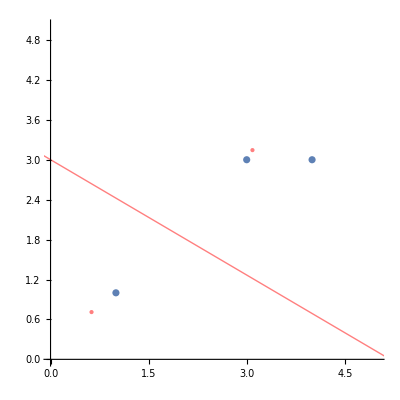

```mathematica
With[{training={{3,3}->1,{4,3}->1,{1,1}->-1}},
cf=Classify[training,Method->{"SupportVectorMachine","KernelType"->"Linear"}];
model=cf[[1]]["Model"];
trainedModel=model["TrainedModel"][[1]];
sv=trainedModel["supportVectors"];
svc=trainedModel["supportVectorCoefficients"];
rho=trainedModel["rho"];
points=training[[All,1]];
sd=StandardDeviation[points];
m=Mean[points];
svadjusted=#*sd+m&/@sv;
(*the y and x intercepts,we still need to un-standardize these*)
plane0={0,rho/Last[(svc.sv)]};
plane1={rho/First[(svc.sv)],0};
Show[ListPlot[training[[All,1]],AspectRatio->1,Epilog->{PointSize[Large],Red,Opacity[.5],Point[svadjusted],InfiniteLine[{plane0*sd+m,plane1*sd+m}]},PlotRange->{{0,5},{0,5}}]]]
(* 可以看出Mathematica支持向量机与书上的方法并不一致！ *)
```

## 例 7.2

```mathematica
Module[{training={{3,3}->1,{4,3}->1,{1,1}->-1},n,X,Y,a,para,p,w,b},
{X,Y,n}={Keys@training,Values@training,Length@training};
a={a1,a2,a3};
para=Last@Minimize[{1/2 Sum[Sum[a[[i]]a[[j]] Y[[i]] Y[[j]](X[[i]].X[[j]]),{i,1,n}],{j,1,n}]-Sum[a[[i]],{i,1,n}],Sum[a[[i]]Y[[i]],{i,1,n}]==0,Sequence@@Table[a[[i]]>=0,{i,1,n}]},a];
p=RandomChoice@Select[Thread[{X,Y}ᵀ->a/.para],#[[2]]>0&];(* 随机选取一个正分量a及对应的x，y *)
w=Sum[a[[i]]Y[[i]]X[[i]],{i,1,n}]/.para;
b=p[[1,2]]-Sum[a[[i]]Y[[i]]Dot[X[[i]],p[[1,1]]],{i,1,n}]/.para;
w.{x1,x2}+b==0]
```

-2+x1/2+x2/2==0

## 例 7.3

```mathematica
Module[{x={x1,x2},z={z1,z2},K,ϕ1,ϕ2},
K[x_,z_]:=(x.z)^2;(* 核方法 *)
ϕ1[x_]:={x[[1]]^2,√2 x[[1]] x[[2]],x[[2]]^2};(* ℋ=ℛ^3 时 *)
ϕ2[x_]:={x[[1]]^2,x[[1]]x[[2]],x[[1]]x[[2]],x[[2]]^2};(* ℋ=ℛ^4 时 *)
{Dot[ϕ1[x],ϕ[z]]===Expand[K[x,z]],Dot[ϕ2[x],ϕ2[z]]===Expand[K[x,z]]}]
```

{True,True}

## 第8章 提升方法

```mathematica
training={0->1,1->1,2->1,3->-1,4->-1,5->-1,6->1,7->1,8->1,9->-1};
X=Keys@training;
Y=Values@training;
n=Length@training;
target=Join[Table[Flatten@{Table[1,i],Table[-1,Total[#]-i]},{i,Accumulate[#]//Most}],Table[Flatten@{Table[-1,i],Table[1,Total[#]-i]},{i,Accumulate[#]//Most}]]&[Length/@TakeList[X,Length/@Split[Y]]];(* .08感谢网友：北京-力学-行跑 帮助*)
w0=Table[1/n,n];
permutations1=Join[Total[w0 Sign@Abs[Y-#]]&/@target,Total[w0 Sign@Abs[Y+#]]&/@target];
e1=permutations1//Min;(* 最小误差率 *)
position1=FirstPosition[permutations1,e1];
g1=Flatten@target[[First@position1]](* 最小误差率分类标准 *)
a1=N@(1/2)Log[(1-Min@e1)/(Min@e1)]
w1=Table[w0[[i]] E^(-a1 Y[[i]]g1[[i]]),{i,n}]/Sum[w0[[i]] E^(-a1 Y[[i]]g1[[i]]),{i,n}]
Total@Unitize[Y-Sign[a1 g1]]
```

{1,1,1,-1,-1,-1,-1,-1,-1,-1}

0.423649

{0.0714286,0.0714286,0.0714286,0.0714286,0.0714286,0.0714286,0.166667,0.166667,0.166667,0.0714286}

3

```mathematica
permutations2=Join[Total[w1 Sign@Abs[Y-#]]&/@target,Total[w1 Sign@Abs[Y+#]]&/@target];
e2=permutations2//Min;
position2=FirstPosition[permutations2,e2];
g2=Flatten@target[[First@position2]]
a2=N@(1/2)Log[(1-Min@e2)/(Min@e2)]
w2=Table[w1[[i]] E^(-a2 Y[[i]]g2[[i]]),{i,n}]/Sum[w1[[i]] E^(-a2 Y[[i]]g2[[i]]),{i,n}]
Total@Unitize[Y-Sign[a1 g1+a2 g2]]
```

{1,1,1,1,1,1,1,1,1,-1}

0.649641

{0.0454545,0.0454545,0.0454545,0.166667,0.166667,0.166667,0.106061,0.106061,0.106061,0.0454545}

3

```mathematica
permutations3=Join[Total[w2 Sign@Abs[Y-#]]&/@target,Total[w2 Sign@Abs[Y+#]]&/@target];(* 误差率 *)
e3=permutations3//Min;
position3=FirstPosition[permutations3,e3];
g3=Flatten@target[[First@position3]]
a3=N@(1/2)Log[(1-Min@e3)/(Min@e3)]
w3=Table[w2[[i]] E^(-a3 Y[[i]]g3[[i]]),{i,n}]/Sum[w2[[i]] E^(-a3 Y[[i]]g3[[i]]),{i,n}]
Total@Unitize[Y-Sign[a1 g1+a2 g2+a3 g3]] (* 此表达式为零时，即全部能正确分类时终止迭代，但不知道如何用NestWhileList表达？ *)
```

{-1,-1,-1,-1,-1,-1,1,1,1,1}

0.752039

{0.125,0.125,0.125,0.101852,0.101852,0.101852,0.0648148,0.0648148,0.0648148,0.125}

0

```mathematica
NestWhileList[,Table[1/n,n],,All]
```